# Mathematica file to compute New Physics contributions to g-2. Acknowledgments should be referred to: Farinaldo S. Queiroz and William Shepherd [arxiv:1403.2309] and M Lindner, M Platscher, FS Queiroz, https://doi.org/10.1016/j.physrep.2017.12.001 [ arXiv:1610.06587v2

New Physics Contribution to (g-2)_μ  
                                                                                    Muon anomalous magnetic moment in a SU (4) ⊗ U (1) X model

Global Parameters. 
Masses of the SM particles in GeV units.

```mathematica
mμ=0.105;(*Muon mass*)mν=0.1*10^-9;(*Neutrino mass*)Mw=80;(*W boson mass*)MZ=90;(*Z mass*)Mh=125;(*Higgs mass*)g=0.65;
v1=246/2;(*because v=u=v''=v1 and we choose v.b2+u.b2+2v''.b2=246.b2*) (*where v2=w=v' is greater than v1*)
sw2=0.231 (*SW^2*);sw=Sqrt[sw2];cw=Sqrt[1-sw2];c2w=cw^2-sw^2;cw2=1-sw2;tgw=sw/cw;θ=0.001(*W-V mixing angle*); t=Sqrt[sw2/(1-4*sw2)];

 t2=t^2; gp=(g*t)/Sqrt[cw2-3*sw2];
```

Experimental Bounds
based on (new):
Current Bound: (261 ± 78) x 10^-11;
Projected Bound:  (261± 34) x 10^-11;

```mathematica
BoundProjectedup=Table[{x,295*10^-11},{x,1,6000,1}];
BoundProjecteddown=Table[{x,227*10^-11},{x,1,6000,1}];
BoundCurrenteup=Table[{x,339*10^-11},{x,1,6000,1}];
BoundCurrentdown=Table[{x,183*10^-11},{x,1,6000,1}];
sigmaCurrent=Table[{x,78*10^-11},{x,1,6000,1}];
sigmaProjected=Table[{x,34*10^-11},{x,1,6000,1}];
```

#### 1. Charged Vector Bosons V1, V2 and V3.

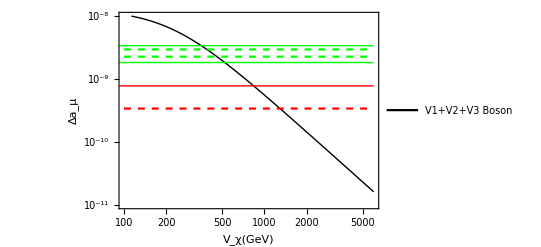

```mathematica
ϵ10=mν/mμ; λ10=mμ/MV;gv10=g/(2*√2);ga10=g/(2*√2);MV=Sqrt[g^2/4*((3*v1^2)+Vqui^2)] ;
(*Where ΔaChargedVec *)
ΔaChargedVec=Table[{Vqui,2.5*(-(gv10^2*mμ^2)/(8*π^2*MV^2)*NIntegrate[(-2*x^2*(1+x-2*ϵ10)+λ10^2*x*(1-x)*(1-ϵ10)^2*(x+ϵ10))/(ϵ10^2*λ10^2*(1-x)*(1-ϵ10^-2*x)+x),{x,0,1}]-(ga10^2*mμ^2)/(8*π^2*MV^2)*NIntegrate[(-2*x^2*(1+x+2*ϵ10)+λ10^2*x*(1-x)*(1+ϵ10)^2*(x-ϵ10))/(ϵ10^2*λ10^2*(1-x)*(1-ϵ10^-2*x)+x),{x,0,1}])},{Vqui,100,6000,10}];
plot10=ListLogLogPlot[{ΔaChargedVec,BoundCurrenteup,BoundCurrentdown,BoundProjectedup,BoundProjecteddown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,6000},{10^-11,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[V,χ ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"V1+V2+V3 Boson"}],{0.7,0.9}]]
```

#### Z’ boson

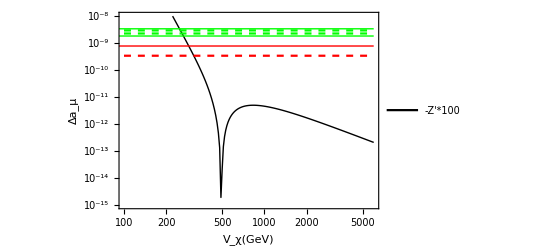

```mathematica
a=v1/V2;
a2=a^2;
A= 3+4t2+(7+4t2)*a^2; 
B=-2*((1+3*t^2)+2*(4+9*t^2)*a^2);
C1=8*(1+4t2)*a2;
Θ=ArcCos[((9*A*B)+(27*C1)+(2*A^3))/(2*(Sqrt[(A^2)+(3*B)])^3)];
λn2= 1/3*(A+(2*Sqrt[A^2 + 3*B]*Cos[((4*Pi)+Θ)/3]));
MZp=Sqrt[(g^2/4*λn2*V2^2)];
D2=2*(7+5*a2)-(3+13*a2)*λn2+2*λn2^2;
x2=-(2*a2)/t*(1-3*t2+(1-t2)*a2-(1-2*t2)*λn2)/D2*w2;
x22=(-(2*a2)/t*(1-3*t2+(1-t2)*a2-(1-2*t2)*λn2)/D2)^2;
y2=1/D2*1/(√3*t)*(2*(2+t^2)*a2-10a2^2*t2-(1+(1-4*t2)*a2)*λn2)*w2; 
y22=(1/D2*1/(√3*t)*(2*(2+t^2)*a2-10a2^2*t2-(1+(1-4*t2)*a2)*λn2))^2;
z2=w2/D2*1/(√6*t)(8*(2+t2)*a2+  4*(3+2 t2)a2^2 -4*(1+2*(2+t2)*a2)* λn2+3*λn2^2);
z22=(1/D2*1/(√6*t)(8*(2+t2)*a2+  4*(3+2 t2)a2^2 -4*(1+2*(2+t2)*a2)* λn2+3*λn2^2))^2;
w2=Sqrt[1/(1+x22+y22+z22)];
(*α=-cw*(-x2+1/Sqrt[3] y2+1/Sqrt[6] z2+4/3 w2*t)+4/3*cw*w2*t; β=-3/Sqrt[6] z2;*)
gv8=(1/2)*( -cw*(-x2+1/(√3)*y2+1/(√6)*z2+4/3*w2*t)+4/3*cw*w2*t-3/(√6)*z2 )*g/(2*cw) ;
ga8=(1/2)*( +cw*(-x2+1/(√3)*y2+1/(√6)*z2+4/3*w2*t)-4/3*cw*w2*t-3/(√6)*z2 )*g/(2*cw) ;
mf8=mμ; ϵ8=mf8/mμ;λ8=mμ/MZp;
ΔaZp=Table[{V2,(gv8^2*mμ^2)/(8*π^2*MZp^2)*NIntegrate[(2*x*(1-x)*(x-2*(1-ϵ8))+λ8^2*(1-ϵ8)^2*x^2*(1+ϵ8-x))/((1-x)*(1-λ8^2*x)+ϵ8^2*λ8^2*x),{x,0,1}] 
+ (ga8^2*mμ^2)/(8*π^2*MZp^2)*NIntegrate[(2*x*(1-x)*(x-2*(1+ϵ8))+λ8^2*(1+ϵ8)^2*x^2*(1-ϵ8-x))/((1-x)*(1-λ8^2*x)+ϵ8^2*λ8^2*x),{x,0,1}] },{V2,100,6000,10}];
size3=Dimensions[ΔaZp];
ΔaZpnew=Table[{ΔaZp[[i,1]],-ΔaZp[[i,2]]*100},{i,1,size3[[1]]}];
ListLogLogPlot[{ΔaZpnew,ΔaZp, BoundCurrenteup,BoundCurrentdown,BoundProjectedup,BoundProjecteddown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Black,Dashed],Directive[Green,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,6000},{10^-15,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[V,χ ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"-Z'*100"}],{0.7,0.9}]]
```

## ZN Boson

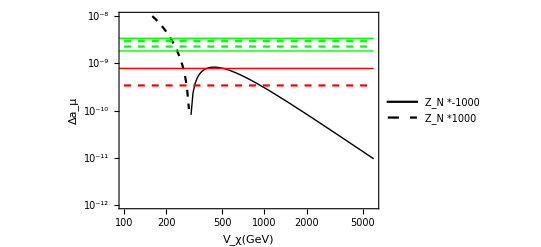

```mathematica
a=v1/V2;
a2=a^2;
λn0= 1/3*(A+(2*Sqrt[A^2 + 3*B]*Cos[Θ/3]));D0=2*(7+5*a2)-(3+13*a2)*λn0+2*λn0^2;
x00=(-(2*a2)/t*(1-3*t2+(1-t2)*a2-(1-2*t2)*λn0)/D0)^2;
y00=(1/D0*1/(√3*t)*(2*(2+t^2)*a2-10a2^2*t2-(1+(1-4*t2)*a2)*λn0))^2;
z00=(1/D0*1/(√6*t)(8*(2+t2)*a2+  4*(3+2 t2)a2^2 -4*(1+2*(2+t2)*a2)* λn0+3*λn0^2))^2;
w0=Sqrt[1/(1+x00+y00+z00)];
x0=-(2*a2)/t*(1-3*t2+(1-t2)*a2-(1-2*t2)*λn0)/D0*w0;
y0=1/D0*1/(√3*t)*(2*(2+t2)*a2-10a2^2*t2-(1+(1-4*t2)*a2)*λn0)*w0; 
z0=1/D0*1/(√6*t)(8*(2+t2)*a2+  4*(3+2 t2)a2^2 -4*(1+2*(2+t2)*a2)* λn0+3*λn0^2)*w0;
MZN=Sqrt[(g^2/4*λn0*V2^2)];
mf9=mμ; ϵ9=mf9/mμ;λ9=mμ/MZN;gv9=1/2*( -cw*(-x0+1/(√3)*y0+1/(√6)*z0+4/3*w0*t)+4/3*cw*w0*t-3/(√6)*z0 )*g/(2*cw) ;
ga9=1/2*( +cw*(-x0+1/(√3)*y0+1/(√6)*z0+4/3*w0*t)-4/3*cw*w0*t-3/(√6)*z0 )*g/(2*cw);
ΔaZN=Table[{V2,(gv9^2*mμ^2)/(8*π^2*MZN^2)*NIntegrate[(2*x*(1-x)*(x-2*(1-ϵ9))+λ9^2*(1-ϵ9)^2*x^2*(1+ϵ9-x))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}] 
+ (ga9^2*mμ^2)/(8*π^2*MZN^2)*NIntegrate[(2*x*(1-x)*(x-2*(1+ϵ9))+λ9^2*(1+ϵ9)^2*x^2*(1-ϵ9-x))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}] },{V2,100,6000,10}];
size19=Dimensions[ΔaZN];
ΔaZNnew=Table[{ΔaZN[[i,1]],-ΔaZN[[i,2]]*1000},{i,1,size19[[1]]}];
ΔaZN1=Table[{ΔaZN[[i,1]],ΔaZN[[i,2]]*1000},{i,1,size19[[1]]}];
ListLogLogPlot[{ΔaZNnew,ΔaZN1,BoundCurrenteup,BoundCurrentdown,BoundProjectedup,BoundProjecteddown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Black,Dashed],Directive[Green,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,6000},{10^-12,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[V,χ ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"Z_N *-1000","Z_N *1000"}],{0.7,0.9}]]
```

#### Doubly Charged Boson

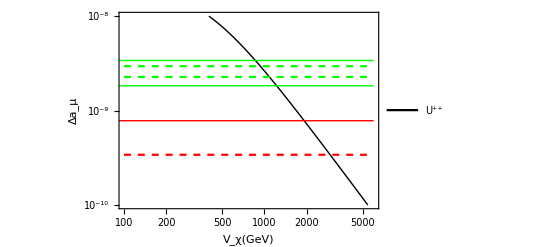

```mathematica
MU=Sqrt[g^2/4*(Vqui^2+9*v1^2)];
mf12=mμ;ϵ12=mf12/mμ; λ12=mμ/MU;
gv12=0;
ga12=g/(2*√2);
ΔaDChargedVec=Table[{Vqui,8*((gv12^2*mμ^2)/(8*π^2*MU^2)*NIntegrate[(-2*x^2*(1+x-2*ϵ12)+λ12^2*x*(1-x)*(1-ϵ12)^2*(x+ϵ12))/(ϵ12^2*λ12^2*(1-x)*(1-ϵ12^-2*x)+x),{x,0,1}]+(ga12^2*mμ^2)/(8*π^2*MU^2)*NIntegrate[(-2*x^2*(1+x+2*ϵ12)+λ12^2*x*(1-x)*(1+ϵ12)^2*(x-ϵ12))/(ϵ12^2*λ12^2*(1-x)*(1-ϵ12^-2*x)+x),{x,0,1}])-
(-4)*((gv12^2*mμ^2)/(8*π^2*MU^2)*NIntegrate[(2*x*(1-x)*(x-2+2*ϵ12)+λ12^2*x^2*(1-ϵ12)^2*(1-x+ϵ12))/((1-x)*(1-λ12^2*x)+ϵ12^2*λ12^2*x),{x,0,1}] 
+ (ga12^2*mμ^2)/(8*π^2*MU^2)*NIntegrate[(2*x*(1-x)*(x-2-2*ϵ12)+λ12^2*x^2*(1+ϵ12)^2*(1-x-ϵ12))/((1-x)*(1-λ12^2*x)+ϵ12^2*λ12^2*x),{x,0,1}] )

},{Vqui,100,6000,10}];
size12=Dimensions[ΔaDChargedVec];
ΔaDChargedVecnew=Table[{ΔaDChargedVec[[i,1]],-ΔaDChargedVec[[i,2]]},{i,1,size12[[1]]}];

(*Plot of the Doubly Charged Vector Boson contribution to Subscript[(g-2), μ] as a function of its mass*)

plot12=ListLogLogPlot[{ΔaDChargedVecnew,BoundCurrenteup,BoundCurrentdown,BoundProjectedup,BoundProjecteddown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,6000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[V,χ ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"U⁺⁺"}],{0.8,0.9}]]
```

COMBINED CONTRIBUTIONS

```mathematica
plottotal1=ListLogLogPlot[{ΔaDChargedVecnew,ΔaChargedVec,ΔaZpnew,ΔaZNnew,ΔaZN1,BoundCurrenteup,BoundProjectedup,sigmaCurrent,sigmaProjected,BoundCurrentdown,BoundProjecteddown},PlotStyle->{Directive[Black,Dashed],Directive[Blue,Thick],Directive[Gray,Dashed],Directive[Orange,Dashed],Directive[Orange,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed],Directive[Green,Thick],Directive[Green,Dashed]},Joined->True,PlotRange->{{100,6000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[V,χ ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->LineLegend[{"U^(++)(-1)","V_1^++V_2^++V_3^+","Z' x(-10^2)","Z_N x(-10^3)","Z_N x(10^3)","Δa_μ Current","Δa_μ Projected","1σ Bound Current","1σ Bound Projected"}],PlotLabel->Style["SU(4)_L⊗ U(1)_X Model with U⁺⁺",14,Black,Bold]]
```

```mathematica
sizetotal=Dimensions[ΔaChargedVec];
sizetotal[[1]];
Totalcontri=Table[{ΔaChargedVec[[i,1]],ΔaChargedVec[[i,2]]+ΔaZp[[i,2]]+ΔaZN[[i,2]]+ΔaDChargedVec[[i,2]]},{i,1,sizetotal[[1]]}];
Totalcontrinew=Table[{Totalcontri[[i,1]],-Totalcontri[[i,2]]},{i,1,sizetotal[[1]]}];
```

```mathematica
plottotal10=ListLogLogPlot[{Totalcontrinew,BoundCurrenteup,BoundProjectedup,sigmaCurrent,sigmaProjected,BoundCurrentdown,BoundProjecteddown},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed],Directive[Green,Thick],Directive[Green,Dashed]},Joined->True,PlotRange->{{500,5000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[V,χ ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->LineLegend[{"Total(-1)","\!\(\*SubscriptBox[\(Δa\), \(μ\)]\) Current","\!\(\*SubscriptBox[\(Δa\), \(μ\)]\) Projected","1σ Bound Current","1σ Bound Projected"}],PlotLabel->Style["SU(4)_L⊗ U(1)_X Model with U⁺⁺",14,Black,Bold]]
```

```mathematica
(*Export["/home/yoxara/Descargas/Figuras/341TotModel.pdf",plottotal10];*)
```